# Project 1 - IX1501

## A project by William Lewin & Elias Chahine

wlewin@kth.se & echahine@kth.se

## 1 - Summary

In the discrete math course you learned how to do a census by computing all possibilities and use the classical definition of probability. In the following problems you are expected to use convolution.
-Graphics-
At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. 

At a fun-fair stall you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

Determine the exact probability function of the sum.

The exact probability function of the sum is calculated using convolution on the separate probability function of each die.

Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

The exact probability of winning teddy prize was calculated by summarizing each discrete value which were a failure requirement. These were then subtracted from the total probability, resulting in the probability of winning a Teddy prize on an individual try.

Determine the expected investment to win a Teddy

The expected investment to win a Teddy was calculated using the average number of tries required to win a Teddy, multiplied with the cost of a single try.

What’s the probability of winning (at least one) Teddy if you play twenty times?

The probability of winning at least one Teddy was calculated by calculating the inverse of not winning any Teddy prize from twenty tries.

## 1 - Mathematic formulas & equations

### Determine the exact probability function of the sum.

Each die is fair in this case, giving an equal chance of landing on each face. 
P(X = k) is then 1/k.

By using Piecewise we can describe each probability function as a separate list of outcomes and probabilities.

DiscreteConvolve was used to merge each probability function as a sum.

### Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

Sum was used to add each discrete point in the ranges.

(1 - Probability of failure) was then used to describe the winning probability by The Law of Total Probability.

### Determine the expected investment to win a Teddy.

The expected number of tries to achieve a success was calculated using 1/(probability of success).

This was then multiplied by the cost of each try.

### What’s the probability of winning (at least one) Teddy if you play twenty times?

The probability of winning at least one in twenty tries was also calculated using the Law of Total Probability, as the probability of not winning anything in twenty tries can easily be calculated:

Binomial Distribution with parameters n = 20, k= 0 and p = probSucess:
(n
k)(p^k(1-p))^(n-k)

## 1 - Discussion

### Explanatory diagrams

#### Plot convolved functions

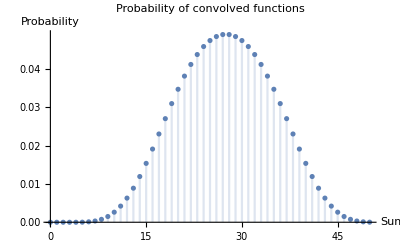

#### Plot of success

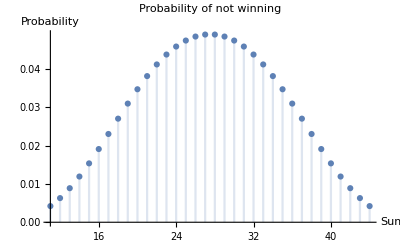
-Graphics-
The probability of winning was deduced from the inverse of the above graph.

### Conclusion & Results

Part one:
pf(Sum) = 
Piecewise[{{1/46080, x==5||x==50}, {1/9216, x==6||x==49}, {1/3072, x==7||x==48}, {7/9216, x==8||x==47}, {23/15360, x==9||x==46}, {121/46080, x==10||x==45}, {97/23040, x==11||x==44}, {29/4608, x==12||x==43}, {409/46080, x==13||x==42}, {61/5120, x==14||x==41}, {707/46080, x==15||x==40}, {293/15360, x==16||x==39}, {53/2304, x==17||x==38}, {311/11520, x==18||x==37}, {95/3072, x==19||x==36}, {1597/46080, x==20||x==35}, {39/1024, x==21||x==34}, {379/9216, x==22||x==33}, {1007/23040, x==23||x==32}, {211/4608, x==24||x==31}, {1091/23040, x==25||x==30}, {223/4608, x==26||x==29}, {1127/23040, 26<x<29}, {0, True}}]

Part two:
Probability of success = 41/3840 = 0.0106771

Part three
Expected investment = 7680/41= 187 €

Part four:
Probability of winning at least once in twenty tries = 0.193208

## 1 - Code

```mathematica
ClearAll["`*"]
```

```mathematica
(*Question number one*)
(*Probability function of each die*)
pyramidfX[k_]=Piecewise[{{1/4,1≤k≤4}}];
cubefX[k_]=Piecewise[{{1/6,1≤k≤6}}];
octafX[k_]:=Piecewise[{{1/8,1≤k≤8}}];
dodefX[k_]:=Piecewise[{{1/12,1≤k≤12}}];
icofX[k_]:=Piecewise[{{1/20,1≤k≤20}}];

(*Convolve each probability function*)
convolutePyramidCube[k_]=DiscreteConvolve[pyramidfX[x],cubefX[x],x,k];
convolutePCOctagon[k_]=DiscreteConvolve[convolutePyramidCube[x],octafX[x],x,k];
convolutePCODodecahedron[k_]= DiscreteConvolve[convolutePCOctagon[x],dodefX[x],x,k];
convolutePCODIcosahedron[k_]=DiscreteConvolve[convolutePCODodecahedron[x],icofX[x],x,k];

(*Plot convolved function*)
DiscretePlot[convolutePCODIcosahedron[x],{x,0,50}];
(*Probability function of sum*)
convolutePCODIcosahedron[x];
```

```mathematica
(*Question number two*)
(*Probability of Failure*)
probFail :=Sum[convolutePCODIcosahedron[x],{x,11,44}];
(*Probability of Failure Plot*)
probFailPlot:=DiscretePlot[convolutePCODIcosahedron[x],{x,11,44}];
(*Probability of success Plot*)
probSucessPlot10:=DiscretePlot[convolutePCODIcosahedron[x],{x,5,10}];
probSucessPlot45:=DiscretePlot[convolutePCODIcosahedron[x],{x,45,50}];
(*Probability of success*)
probSucess:= 1-probFail;
```

```mathematica
Print["Probability of failure = ",probFail , " = ", N[probFail]]
Print["Probability of success = ",probSucess, " = ", N[probSucess]]
```

Probability of failure = 3799/3840 = 0.989323

Probability of success = 41/3840 = 0.0106771

```mathematica
(*Question number three*)
tryPrice := 2;
(*Expected number of trials until success*)
expectedTrials:= 1/probSucess; 
expectedInvestment := expectedTrials*tryPrice;
Print["Expected investment = ",expectedInvestment, " = ", Round[expectedInvestment], " €"]
```

Expected investment = 7680/41 = 187 €

```mathematica
(*Question number four*)
tries:= 20;
wins := 0;
(*Binomial Distribution*)
probNotWinning= Binomial[tries,wins]*(probSucess^(wins))*((1-probSucess)^(tries-wins));
probWinning = 1-probNotWinning;
Print["Probability of winning atleast once = ", probWinning, " = " , N[probWinning]]
```

Probability of winning atleast once = (93896720713692929068924170210101909985514754789674511350420879336475999/485986815555701405566977235358756074107883642001817600000000000000000000) = 0.193208

## 11 - Summary

Since we have the exact probabilities we can compare with the approximate answer given by the normal distribution.

Determine the expectation value and standard deviation of the distribution in the Teddy case.

Determine the probability of the Teddy prize using the normal distribution.

Compare and comment on the results.

## 11 - Mathematic formulas & equations

## 11 - Discussion

## 11 - Code

```mathematica
(*Part one, by the definition of the Expected value*)
Sum[x*convolutePCODIcosahedron[x],{x,0,50}]
```

55/2

```mathematica
(*Part two*)
```